## Automated process for creating graphical representation with the Wigner-D functions

```mathematica
ClearAll["Global`*"]
```

### Author: Robert Poenaru Date: 25th August 🗓

### Constant spin for a system

```mathematica
spin=3;
theta=π/3;
phi=π/6;
psi=π/2;
```

Create a set of projections M and K,  for a given spin I

```mathematica
wfComp[spin_]:=Table[{spin,m,k},{m,-spin,spin},{k,-spin,spin}];
```

Generate a set of Euler Angles using a pure function

```mathematica
angles[]={RandomReal[{π/6,π}],RandomReal[{π/6,π}],RandomReal[{π/6,π}]};
```

Create the first state φ_0=|I M=-I K=-I>

```mathematica
state0=wfComp[spin][[1]];
```

```mathematica
printer[state_]:=Do[Print["|IMK> = ","|",state[[i,1]]," ",state[[i,2]]," ",state[[i,3]]," >"],{i,1,2*spin+1}];
printer[state0]
```

|IMK> = |3 -3 -3 >

|IMK> = |3 -3 -2 >

|IMK> = |3 -3 -1 >

|IMK> = |3 -3 0 >

|IMK> = |3 -3 1 >

|IMK> = |3 -3 2 >

|IMK> = |3 -3 3 >

```mathematica
wigner[state_]:=Table[Re[WignerD[state[[i]],angles[][[1]],angles[][[2]],angles[][[3]]]],{i,1,2*spin+1}];
```

```mathematica
wigner[state0]
```

{-0.00156159,0.0241524,0.128375,0.237162,0.0685892,-0.382753,-0.498086}

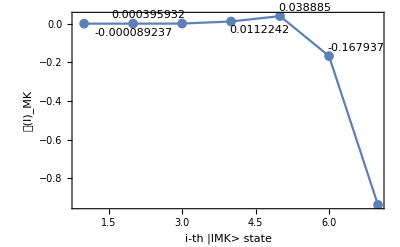

```mathematica
ListPlot[Labeled[#,#]&/@Table[wigner[state0][[i]],{i,1,Length[wigner[state0]]}],PlotRange->Full,Axes->False,Frame->True,PlotMarkers->{Automatic, Medium},Joined->True,FrameLabel->{"i-th |IMK> state","𝒟(I)_MK"}]
```